{0.,0.3,0.337,0.5,0.837,0.637}

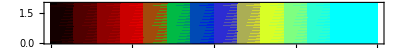

```mathematica
Varying strength strokewise;
ENE6[n6_,g6_,p6_,L6_]:=38.19/(L6^2)*((n6*Pi)^2-(4/g6)*((Sin[n6*Pi*p6])^2)-(4/(g6*n6*Pi)^2)*((Sin[n6*Pi*p6])^4+(2*Pi*n6)*(1-2*p6)*((Sin[n6*Pi*p6])^3)*Cos[n6*Pi*p6]));
(*This in electron volt
0.0423 is the value of h^2/2mL^2  in meV ie in milli electron volt where h cut is taken in electrol volt and m is mass of e , L = 30nm**)
(*Now lets define PArtition function for pertubative   ENE6rgy*)
ZA6[p6_,st6_,T6_,L6_]:=Sum[Exp[-(38.19/((L6^2)T6))*((n6*Pi)^2-(4/st6)*((Sin[n6*Pi*p6])^2)-(4/(st6*n6*Pi)^2)*((Sin[n6*Pi*p6])^4+(2*Pi*n6)*(1-2*p6)*((Sin[n6*Pi*p6])^3)*Cos[n6*Pi*p6]))],{n6,1,100}](*Note that Wh  ENE6ver T is written then the boltzman Constant is also included in it*)
(*Defining Temperature, in all these values boltzman const is included*)
(*if ur temperature is x then put x*0.086173333      *)
  atc6 =   0.12926;(* K multiplied by Cold reservoir temperature  here it is 1.5 K*) 
  ath6 =0.43086665;(*Hot reservoir 1 temp *  5K *) 
  ath7 = 1.02546263;(* Hot reservoir 2 temp *11.9K *)
  ath8 =2.1543333;(*Hot reservoir 3 temp *K 25 *)
  asth6 =1;(*Strength at hot reservoir*)
  astc6 =-1;(* strength in cold reservoir *)
  k = 0.08617; (*Value of boltzman constant in meV*)


Work varying position and length cyclewise;
colors={Black,Red,Green,Blue,Cyan,Yellow};

w=List@@@ColorConvert[colors,"RGB"].{0.3,0.3370,0.5}

colorfn=Evaluate[Blend[{w,colors}ᵀ,#]]&;

DensityPlot[x,{x,0,1},{y,0,2},AspectRatio->0.1,ColorFunction->colorfn]
```

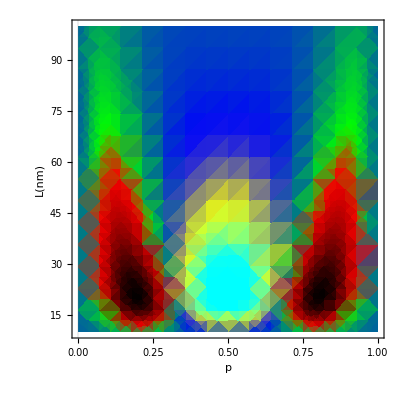

```mathematica
DensityPlot[((Sum[  ENE6[n6,asth6,p6,L]/(Exp[  ENE6[n6,asth6,p6,L]/ath8]),{n6,1,100}]/ZA6[p6,asth6,ath8,L])- (Sum[  ENE6[n6,asth6,p6,L]/(Exp[(  ENE6[n6,astc6,p6,L])/atc6 ]),{n6,1,100}]/ZA6[p6,astc6,atc6 ,L])-(Sum[  ENE6[n6,astc6,p6,L]/(Exp[(  ENE6[n6,asth6,p6,L])/ath8]),{n6,1,100}]/ZA6[p6,asth6,ath8,L])+(Sum[  ENE6[n6,astc6,p6,L]/(Exp[(  ENE6[n6,astc6,p6,L])/atc6 ]),{n6,1,100}]/ZA6[p6,astc6,atc6 ,L])),{p6,0,1},{L,10,100},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"p","L(nm)"},LabelStyle->{FontSize ->25,Directive[Bold]},PlotLegends->BarLegend[Automatic,LegendMarkerSize->180,LegendFunction->"Frame",LegendMargins->5,LegendLabel->"W(meV)"],ColorFunction->colorfn]
```

```mathematica
Export["impu81.pdf",-Graphics-]
```

impu81.pdf

```mathematica
SystemOpen["impu81.pdf"]
```

impu82.pdf

```mathematica
Import["impu82.pdf"]
```

Import::general: Unsupported Shading type 7

Import::general: Could not create shading pattern

Import::general: Could not create pattern from /p5

General::stop: Further output of Import::general will be suppressed during this calculation.

$Failed

```mathematica
SystemOpen["impu81.pdf"]
```

## varying position and Th L = 25nm

{0.,0.3,0.337,0.8,0.837}

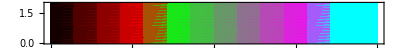

```mathematica
L= 25;
```

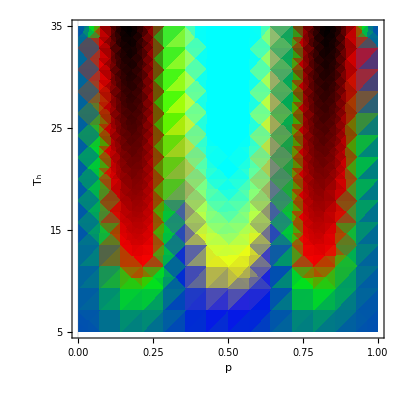

```mathematica
DensityPlot[((Sum[  ENE6[n6,asth6,p6,L]/(Exp[  ENE6[n6,asth6,p6,L]/(k*T)]),{n6,1,100}]/ZA6[p6,asth6,(k*T),L])- (Sum[  ENE6[n6,asth6,p6,L]/(Exp[(  ENE6[n6,astc6,p6,L])/atc6 ]),{n6,1,100}]/ZA6[p6,astc6,atc6 ,L])-(Sum[  ENE6[n6,astc6,p6,L]/(Exp[(  ENE6[n6,asth6,p6,L])/(k*T)]),{n6,1,100}]/ZA6[p6,asth6,(k*T),L])+(Sum[  ENE6[n6,astc6,p6,L]/(Exp[(  ENE6[n6,astc6,p6,L])/atc6 ]),{n6,1,100}]/ZA6[p6,astc6,atc6 ,L])),{p6,0,1},{T,5,35},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"p",Subscript["T","h"]},LabelStyle->{FontSize ->25,Directive[Bold]},FrameTicks->{{{5,15,25,35},None},{Automatic,None}},PlotLegends->BarLegend[Automatic,LegendMarkerSize->180,LegendFunction->"Frame",LegendMargins->5,LegendLabel->"W(meV)"],ColorFunction->colorfn]
```

```mathematica
Export["impu82.pdf",-Graphics-]
```

impu82.pdf

```mathematica
SystemOpen["impu82.pdf"]
```

```mathematica
SystemOpen["impu82.pdf"]
```

```mathematica
SystemOpen["impu82.pdf"]
```

## Varying f and Th (from 1 to 50K)

```mathematica
ph= 0.5;
```

{0.3,0.657,0.457}

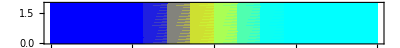

```mathematica
colors={Blue,Cyan,Yellow};

w=List@@@ColorConvert[colors,"RGB"].{0.1,0.3570,0.3}

colorfn2=Evaluate[Blend[{w,colors}ᵀ,#]]&;


DensityPlot[x,{x,0,1},{y,0,2},AspectRatio->0.1,ColorFunction->colorfn2]
```

```mathematica
{0.5,0.837,0.637}
```

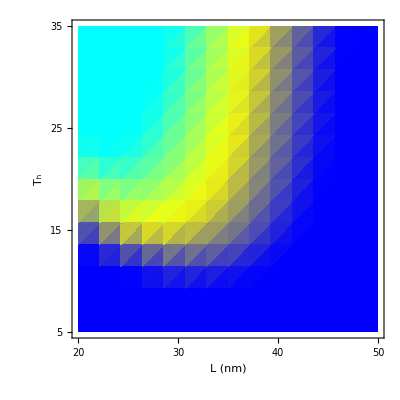

```mathematica
DensityPlot[((Sum[  ENE6[n6,asth6,ph,Lth]/(Exp[  ENE6[n6,asth6,ph,Lth]/(k*T)]),{n6,1,100}]/ZA6[ph,asth6,(k*T),Lth])- (Sum[  ENE6[n6,asth6,ph,Lth]/(Exp[(  ENE6[n6,astc6,ph,Lth])/atc6 ]),{n6,1,100}]/ZA6[ph,astc6,atc6 ,Lth])-(Sum[  ENE6[n6,astc6,ph,Lth]/(Exp[(  ENE6[n6,asth6,ph,Lth])/(k*T)]),{n6,1,100}]/ZA6[ph,asth6,(k*T),Lth])+(Sum[  ENE6[n6,astc6,ph,Lth]/(Exp[(  ENE6[n6,astc6,ph,Lth])/atc6 ]),{n6,1,100}]/ZA6[ph,astc6,atc6 ,Lth])),{Lth,20,50},{T,5,35},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"L (nm)",Subscript["T","h"]},LabelStyle->{FontSize ->25,Directive[Bold]},FrameTicks->{{{5,15,25,35},None},{{20,30,40,50},None}},PlotLegends->BarLegend[Automatic,LegendMarkerSize->180,LegendFunction->"Frame",LegendMargins->5,LegendLabel->"W(meV)"],ColorFunction->colorfn2]
```

```mathematica
Export["img.pdf",-Graphics-]
```

img.pdf

```mathematica
SystemOpen["img.pdf"]
```

```mathematica
SystemOpen["impu131.pdf"]
```

impu131.pdf

```mathematica
SystemOpen["impu131.pdf"]
```

## For Cold Pump , plotting work in the above plot just by putting p =0.15

{0.,0.15,0.7757}

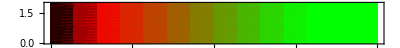

```mathematica
ph= 0.15;


colors={Black,Red,Green};

w=List@@@ColorConvert[colors,"RGB"].{0.15,0.77570,0.1}

colorfn3=Evaluate[Blend[{w,colors}ᵀ,#]]&;


DensityPlot[x,{x,0,1},{y,0,2},AspectRatio->0.1,ColorFunction->colorfn3]
```

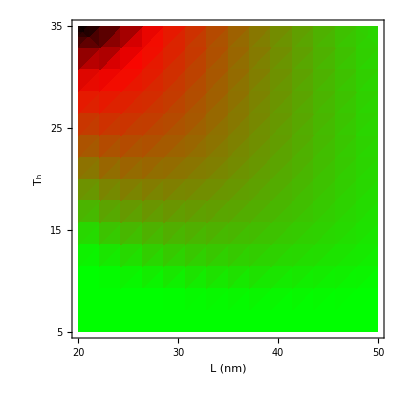

```mathematica
DensityPlot[((Sum[  ENE6[n6,asth6,ph,Lth]/(Exp[  ENE6[n6,asth6,ph,Lth]/(k*T)]),{n6,1,100}]/ZA6[ph,asth6,(k*T),Lth])- (Sum[  ENE6[n6,asth6,ph,Lth]/(Exp[(  ENE6[n6,astc6,ph,Lth])/atc6 ]),{n6,1,100}]/ZA6[ph,astc6,atc6 ,Lth])-(Sum[  ENE6[n6,astc6,ph,Lth]/(Exp[(  ENE6[n6,asth6,ph,Lth])/(k*T)]),{n6,1,100}]/ZA6[ph,asth6,(k*T),Lth])+(Sum[  ENE6[n6,astc6,ph,Lth]/(Exp[(  ENE6[n6,astc6,ph,Lth])/atc6 ]),{n6,1,100}]/ZA6[ph,astc6,atc6 ,Lth])),{Lth,20,50},{T,5,35},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"L (nm)",Subscript["T","h"]},LabelStyle->{FontSize ->25,Directive[Bold]},FrameTicks->{{{5,15,25,35},None},{{20,30,40,50},None}},PlotLegends->BarLegend[Automatic,LegendMarkerSize->180,LegendFunction->"Frame",LegendMargins->5,LegendLabel->"W(meV)"],ColorFunction->colorfn3]
```

```mathematica
Export["impu132.pdf",-Graphics-]
```

impu132.pdf

```mathematica
SystemOpen["impu132.pdf"]
```

```mathematica
SystemOpen["impu132.pdf"]
```

ds.pdf

impu132.pdf

```mathematica
SystemOpen["impu132.pdf"]
```

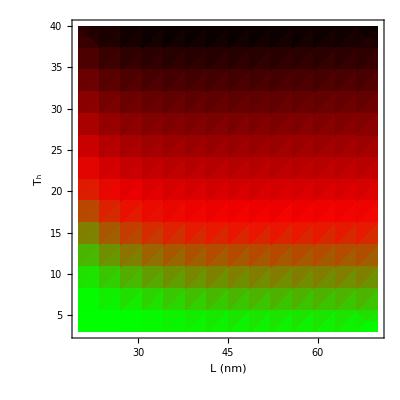

```mathematica
DensityPlot[(-(Sum[  ENE6[n6,astc6,ph,Lth]/(Exp[(  ENE6[n6,asth6,ph,Lth])/(k*T)]),{n6,1,100}]/ZA6[ph,asth6,(k*T),Lth])+(Sum[  ENE6[n6,astc6,ph,Lth]/(Exp[(  ENE6[n6,astc6,ph,Lth])/atc6 ]),{n6,1,100}]/ZA6[ph,astc6,atc6 ,Lth])),{Lth,20,70},{T,3,40},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"L (nm)",Subscript["T","h"]},LabelStyle->{FontSize ->25,Directive[Bold]},PlotLegends->BarLegend[Automatic,LegendMarkerSize->180,LegendFunction->"Frame",LegendMargins->5,LegendLabel->"Qout(meV)"],ColorFunction->colorfn4]
```

## Efficiency(varying L and P)

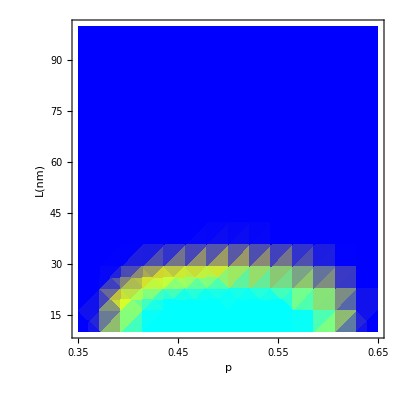

```mathematica
p1 =DensityPlot[((Sum[  ENE6[n6,asth6,p6,L]/(Exp[  ENE6[n6,asth6,p6,L]/ath8]),{n6,1,100}]/ZA6[p6,asth6,ath8,L])- (Sum[  ENE6[n6,asth6,p6,L]/(Exp[(  ENE6[n6,astc6,p6,L])/atc6 ]),{n6,1,100}]/ZA6[p6,astc6,atc6 ,L])-(Sum[  ENE6[n6,astc6,p6,L]/(Exp[(  ENE6[n6,asth6,p6,L])/ath8]),{n6,1,100}]/ZA6[p6,asth6,ath8,L])+(Sum[  ENE6[n6,astc6,p6,L]/(Exp[(  ENE6[n6,astc6,p6,L])/atc6 ]),{n6,1,100}]/ZA6[p6,astc6,atc6 ,L]))/((Sum[  ENE6[n6,asth6,p6,L]/(Exp[  ENE6[n6,asth6,p6,L]/ath8]),{n6,1,100}]/ZA6[p6,asth6,ath8,L])- (Sum[  ENE6[n6,asth6,p6,L]/(Exp[(  ENE6[n6,astc6,p6,L])/atc6 ]),{n6,1,100}]/ZA6[p6,astc6,atc6 ,L])),{p6,0.35,0.65},{L,10,100},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"p","L(nm)"},LabelStyle->{FontSize ->25,Directive[Bold]},FrameTicks->{{Automatic,None},{{0.35,0.45,0.55,0.65},None}},PlotLegends->BarLegend[Automatic,LegendMarkerSize->180,LegendFunction->"Frame",LegendMargins->5,LegendLabel->"η"],ColorFunction->colorfn2]
```

```mathematica
Export["impu84.pdf",-Graphics-]
```

impu84.pdf

```mathematica
SystemOpen["impu84.pdf"]
```

```mathematica
SystemOpen["impu84.pdf"]
```

```mathematica
SystemOpen["impu84.pdf"]
```

```mathematica
SystemOpen["impu84.pdf"]
```

## Efficiency(varying L and Th)

```mathematica
ph6 = 0.5;
```

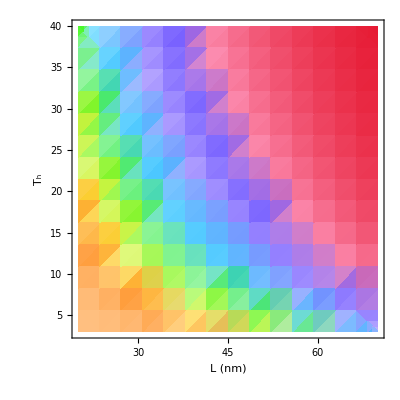

impu85.pdf

```mathematica
DensityPlot[((Sum[  ENE6[n6,asth6,ph6,L]/(Exp[  ENE6[n6,asth6,ph6,L]/(k*T)]),{n6,1,100}]/ZA6[ph6,asth6,(k*T),L])- (Sum[  ENE6[n6,asth6,ph6,L]/(Exp[(  ENE6[n6,astc6,ph6,L])/atc6 ]),{n6,1,100}]/ZA6[ph6,astc6,atc6 ,L])-(Sum[  ENE6[n6,astc6,ph6,L]/(Exp[(  ENE6[n6,asth6,ph6,L])/(k*T)]),{n6,1,100}]/ZA6[ph6,asth6,(k*T),L])+(Sum[  ENE6[n6,astc6,ph6,L]/(Exp[(  ENE6[n6,astc6,ph6,L])/atc6 ]),{n6,1,100}]/ZA6[ph6,astc6,atc6 ,L]))/((Sum[  ENE6[n6,asth6,ph6,L]/(Exp[  ENE6[n6,asth6,ph6,L]/(k*T)]),{n6,1,100}]/ZA6[ph6,asth6,(k*T),L])- (Sum[  ENE6[n6,asth6,ph6,L]/(Exp[(  ENE6[n6,astc6,ph6,L])/atc6 ]),{n6,1,100}]/ZA6[ph6,astc6,atc6 ,L])),{L,20,70},{T,3,40},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"L (nm)",Subscript["T","h"]},LabelStyle->{FontSize ->25,Directive[Bold]},PlotLegends->BarLegend[Automatic,LegendMarkerSize->180,LegendFunction->"Frame",LegendMargins->5,LegendLabel->"η"],ColorFunction->"BrightBands"]
```

```mathematica
SystemOpen["impu85.pdf"]
```

## Efficiency varying Th and P

```mathematica
Lthc = 25;
```

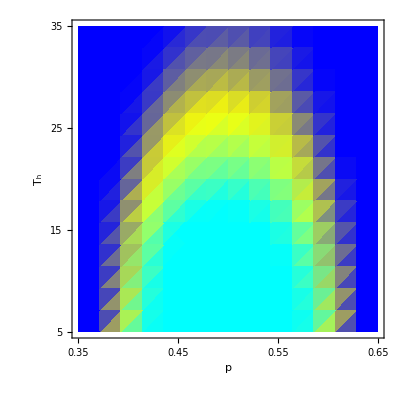

```mathematica
DensityPlot[((Sum[  ENE6[n6,asth6,p,Lthc]/(Exp[  ENE6[n6,asth6,p,Lthc]/(k*T)]),{n6,1,100}]/ZA6[p,asth6,(k*T),Lthc])- (Sum[  ENE6[n6,asth6,p,Lthc]/(Exp[(  ENE6[n6,astc6,p,Lthc])/atc6 ]),{n6,1,100}]/ZA6[p,astc6,atc6 ,Lthc])-(Sum[  ENE6[n6,astc6,p,Lthc]/(Exp[(  ENE6[n6,asth6,p,Lthc])/(k*T)]),{n6,1,100}]/ZA6[p,asth6,(k*T),Lthc])+(Sum[  ENE6[n6,astc6,p,Lthc]/(Exp[(  ENE6[n6,astc6,p,Lthc])/atc6 ]),{n6,1,100}]/ZA6[p,astc6,atc6 ,Lthc]))/((Sum[  ENE6[n6,asth6,p,Lthc]/(Exp[  ENE6[n6,asth6,p,Lthc]/(k*T)]),{n6,1,100}]/ZA6[p,asth6,(k*T),Lthc])- (Sum[  ENE6[n6,asth6,p,Lthc]/(Exp[(  ENE6[n6,astc6,p,Lthc])/atc6 ]),{n6,1,100}]/ZA6[p,astc6,atc6 ,Lthc])),{p,0.35,0.65},{T,5,35},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"p",Subscript["T","h"]},LabelStyle->{FontSize ->25,Directive[Bold]},FrameTicks->{{{5,15,25,35},None},{{0.35,0.45,0.55,0.65},None}},PlotLegends->BarLegend[Automatic,LegendMarkerSize->180,LegendFunction->"Frame",LegendMargins->5,LegendLabel->"η"],ColorFunction-> colorfn2]
```

```mathematica
Export["impu86.pdf",-Graphics-]
```

impu86.pdf

```mathematica
SystemOpen["impu86.pdf"]
```

```mathematica
SystemOpen["impu86.pdf"]
```

```mathematica
SystemOpen["impu86.pdf"]
```

```mathematica
SystemOpen["impu86.pdf"]
```

impu85.pdf

```mathematica
SystemOpen["impu85.pdf"]
```

```mathematica
Export["dens12.pdf",
```

dens12.pdf

```mathematica
E
```

dens7.pdf

```mathematica
SystemOpen["dens7.pdf",
```

SystemOpen::argx: SystemOpen called with 2 arguments; 1 argument is expected.

```mathematica
SystemOpen["dens7.pdf",
```

dens7.pdf

```mathematica
SystemOpen["dens8.pdf"]
```

```mathematica
SystemOpen["dens7.pdf"]
```

## Qin For Heat ingine

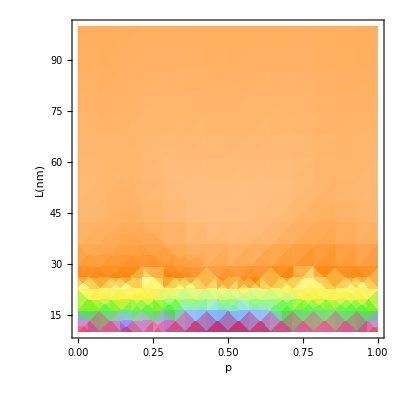

```mathematica
DensityPlot[(Sum[  ENE6[n6,asth6,p6,L]/(Exp[  ENE6[n6,asth6,p6,L]/ath8]),{n6,1,100}]/ZA6[p6,asth6,ath8,L])- (Sum[  ENE6[n6,asth6,p6,L]/(Exp[(  ENE6[n6,astc6,p6,L])/atc6 ]),{n6,1,100}]/ZA6[p6,astc6,atc6 ,L]),{p6,0,1},{L,10,100},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{p,"L(nm)"},LabelStyle->{FontSize ->25,Directive[Bold]},PlotLegends->BarLegend[Automatic,LegendMarkerSize->180,LegendFunction->"Frame",LegendMargins->5,LegendLabel->Subscript["Q","in"]],ColorFunction->"BrightBands"]
```

## Qout for heat engine

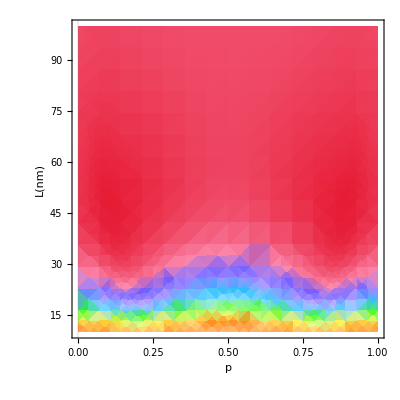

```mathematica
DensityPlot[-(Sum[  ENE6[n6,astc6,p6,L]/(Exp[(  ENE6[n6,asth6,p6,L])/ath8]),{n6,1,100}]/ZA6[p6,asth6,ath8,L])+(Sum[  ENE6[n6,astc6,p6,L]/(Exp[(  ENE6[n6,astc6,p6,L])/atc6 ]),{n6,1,100}]/ZA6[p6,astc6,atc6 ,L]),{p6,0,1},{L,10,100},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{p,"L(nm)"},LabelStyle->{FontSize ->25,Directive[Bold]},PlotLegends->BarLegend[Automatic,LegendMarkerSize->180,LegendFunction->"Frame",LegendMargins->5,LegendLabel->Subscript["Q","out"]],ColorFunction->"BrightBands"]
```

## Qin for heat engine

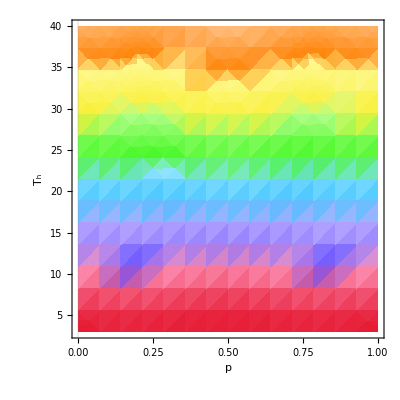

impu90.pdf

```mathematica
DensityPlot[(Sum[  ENE6[n6,asth6,p6,L]/(Exp[  ENE6[n6,asth6,p6,L]/(k*T)]),{n6,1,100}]/ZA6[p6,asth6,(k*T),L])- (Sum[  ENE6[n6,asth6,p6,L]/(Exp[(  ENE6[n6,astc6,p6,L])/atc6 ]),{n6,1,100}]/ZA6[p6,astc6,atc6 ,L]),{p6,0,1},{T,3,40},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"p",Subscript["T","h"]},LabelStyle->{FontSize ->25,Directive[Bold]},PlotLegends->BarLegend[Automatic,LegendMarkerSize->180,LegendFunction->"Frame",LegendMargins->5,LegendLabel->Subscript["Q","in"]],ColorFunction->"BrightBands"]
```

```mathematica
SystemOpen["impu90.pdf"]
```

## Qout for heat engine

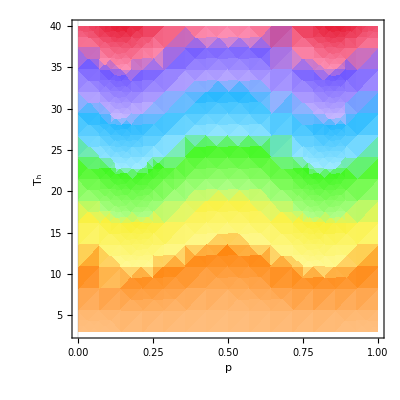

```mathematica
DensityPlot[-(Sum[  ENE6[n6,astc6,p6,L]/(Exp[(  ENE6[n6,asth6,p6,L])/(k*T)]),{n6,1,100}]/ZA6[p6,asth6,(k*T),L])+(Sum[  ENE6[n6,astc6,p6,L]/(Exp[(  ENE6[n6,astc6,p6,L])/atc6 ]),{n6,1,100}]/ZA6[p6,astc6,atc6 ,L]),{p6,0,1},{T,3,40},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"p",Subscript["T","h"]},LabelStyle->{FontSize ->25,Directive[Bold]},PlotLegends->BarLegend[Automatic,LegendMarkerSize->180,LegendFunction->"Frame",LegendMargins->5,LegendLabel->Subscript["Q","out"]],ColorFunction->"BrightBands"]
```

# COP for COLD PUMP

# Th vs P

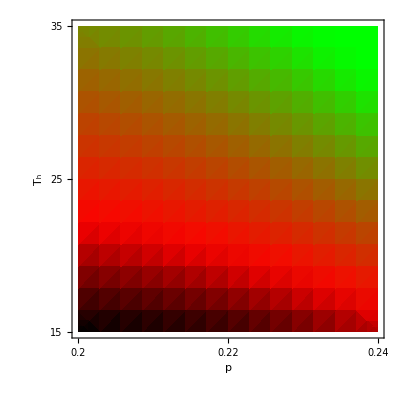

```mathematica
DensityPlot[-(-(Sum[  ENE6[n6,astc6,p6,L]/(Exp[(  ENE6[n6,asth6,p6,L])/(k*T)]),{n6,1,100}]/ZA6[p6,asth6,(k*T),L])+(Sum[  ENE6[n6,astc6,p6,L]/(Exp[(  ENE6[n6,astc6,p6,L])/atc6 ]),{n6,1,100}]/ZA6[p6,astc6,atc6 ,L]))/(-((Sum[  ENE6[n6,asth6,p6,L]/(Exp[  ENE6[n6,asth6,p6,L]/(k*T)]),{n6,1,100}]/ZA6[p6,asth6,(k*T),L])- (Sum[  ENE6[n6,asth6,p6,L]/(Exp[(  ENE6[n6,astc6,p6,L])/atc6 ]),{n6,1,100}]/ZA6[p6,astc6,atc6 ,L])-(Sum[  ENE6[n6,astc6,p6,L]/(Exp[(  ENE6[n6,asth6,p6,L])/(k*T)]),{n6,1,100}]/ZA6[p6,asth6,(k*T),L])+(Sum[  ENE6[n6,astc6,p6,L]/(Exp[(  ENE6[n6,astc6,p6,L])/atc6 ]),{n6,1,100}]/ZA6[p6,astc6,atc6 ,L]))),{p6,0.2,0.24},{T,15,35},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"p",Subscript["T","h"]},LabelStyle->{FontSize ->25,Directive[Bold]},FrameTicks->{{{5,15,25,35},None},{{0.2,0.22,0.24},None}},PlotLegends->BarLegend[Automatic,LegendMarkerSize->180,LegendFunction->"Frame",LegendMargins->5,LegendLabel->"COP"],ColorFunction->colorfn3]
```

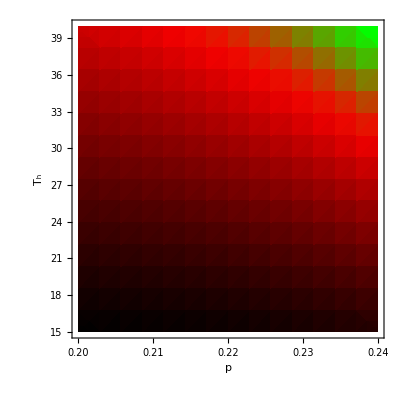
```mathematica
Export["impu187.pdf",-Graphics- ]
```

impu187.pdf

```mathematica
SystemOpen["impu187.pdf"]
```

25 Cop for p vs

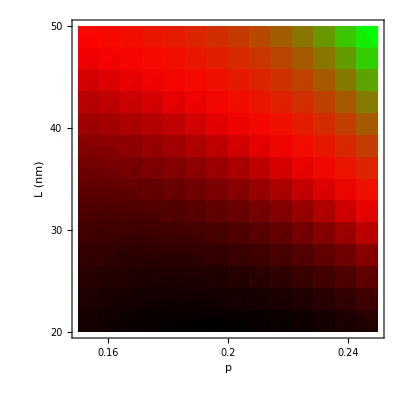

```mathematica
Cop for L vs p
DensityPlot[-(-(Sum[  ENE6[n6,astc6,p6,L]/(Exp[(  ENE6[n6,asth6,p6,L])/ath8]),{n6,1,100}]/ZA6[p6,asth6,ath8,L])+(Sum[  ENE6[n6,astc6,p6,L]/(Exp[(  ENE6[n6,astc6,p6,L])/atc6 ]),{n6,1,100}]/ZA6[p6,astc6,atc6 ,L]))/(-((Sum[  ENE6[n6,asth6,p6,L]/(Exp[  ENE6[n6,asth6,p6,L]/ath8]),{n6,1,100}]/ZA6[p6,asth6,ath8,L])- (Sum[  ENE6[n6,asth6,p6,L]/(Exp[(  ENE6[n6,astc6,p6,L])/atc6 ]),{n6,1,100}]/ZA6[p6,astc6,atc6 ,L])-(Sum[  ENE6[n6,astc6,p6,L]/(Exp[(  ENE6[n6,asth6,p6,L])/ath8]),{n6,1,100}]/ZA6[p6,asth6,ath8,L])+(Sum[  ENE6[n6,astc6,p6,L]/(Exp[(  ENE6[n6,astc6,p6,L])/atc6 ]),{n6,1,100}]/ZA6[p6,astc6,atc6 ,L]))),{p6,0.15,0.25},{L,20,50},FrameTicks->{{{20,30,40,50},None},{{0.16,0.20,0.24},None}},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"p","L (nm)"},LabelStyle->{FontSize ->25,Directive[Bold]},PlotLegends->BarLegend[Automatic,LegendMarkerSize->180,LegendFunction->"Frame",LegendMargins->5,LegendLabel->"COP"],ColorFunction->colorfn3]
```

```mathematica
Export["impu187.pdf",-Graphics-]
```

impu187.pdf

```mathematica
SystemOpen["impu187.pdf"]
```

```mathematica
SystemOpen["impu186.pdf"]
```

```mathematica
Export["impu1871.pdf",-Graphics- ]
```

impu1871.pdf

```mathematica
SystemOpen["impu1871.pdf"]
```

```mathematica
SystemOpen["impu187.pdf"]
```

```mathematica
SystemOpen["impu186.pdf"]
```

```mathematica
Export["",]
```

```mathematica
Show[p1,p2,p3,PlotRange->All]
```

```mathematica
Export["impu91.pdf",
```

impu91.pdf

```mathematica
SystemOpen["impu91.pdf"]
```

```mathematica
SystemOpen["impu90.pdf"]
```

```mathematica
SystemOpen["impu89.pdf"]
```

```mathematica
SystemOpen["impu88.pdf"]
```

```mathematica
SystemOpen["impu86.pdf"]
```

```mathematica
SystemOpen["impu85.pdf"]
```

```mathematica
SystemOpen["impu85.pdf"]
```

```mathematica
SystemOpen["impu83.pdf"]
```

```mathematica
SystemOpen["impu82.pdf"]
```

```mathematica
SystemOpen["impu81.pdf"]
```

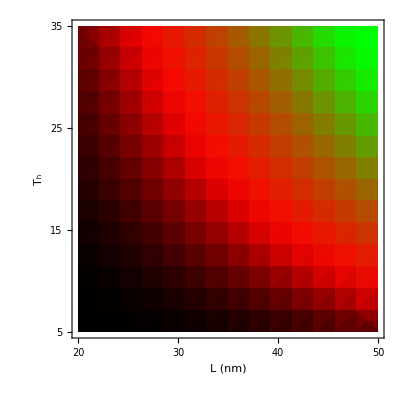

```mathematica
DensityPlot[-(-(Sum[  ENE6[n6,astc6,ph,Lth]/(Exp[(  ENE6[n6,asth6,ph,Lth])/(k*T)]),{n6,1,100}]/ZA6[ph,asth6,(k*T),Lth])+(Sum[  ENE6[n6,astc6,ph,Lth]/(Exp[(  ENE6[n6,astc6,ph,Lth])/atc6 ]),{n6,1,100}]/ZA6[ph,astc6,atc6 ,Lth]))/(-(((Sum[  ENE6[n6,asth6,ph,Lth]/(Exp[  ENE6[n6,asth6,ph,Lth]/(k*T)]),{n6,1,100}]/ZA6[ph,asth6,(k*T),Lth])- (Sum[  ENE6[n6,asth6,ph,Lth]/(Exp[(  ENE6[n6,astc6,ph,Lth])/atc6 ]),{n6,1,100}]/ZA6[ph,astc6,atc6 ,Lth])-(Sum[  ENE6[n6,astc6,ph,Lth]/(Exp[(  ENE6[n6,asth6,ph,Lth])/(k*T)]),{n6,1,100}]/ZA6[ph,asth6,(k*T),Lth])+(Sum[  ENE6[n6,astc6,ph,Lth]/(Exp[(  ENE6[n6,astc6,ph,Lth])/atc6 ]),{n6,1,100}]/ZA6[ph,astc6,atc6 ,Lth])))),{Lth,20,50},{T,5,35},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"L (nm)",Subscript["T","h"]},LabelStyle->{FontSize ->25,Directive[Bold]},FrameTicks->{{{5,15,25,35},None},{{20,30,40,50},None}},PlotLegends->BarLegend[Automatic,LegendMarkerSize->180,LegendFunction->"Frame",LegendMargins->5,LegendLabel->"COP)"],ColorFunction->colorfn3]
```